Ricci scalar R = -1/(r^3 w^4)2 ⅇ^(-(r-R0)^2/w^2) ((ⅇ^((r-R0) ((2 A ⅇ^(-(r-R0)^2/w^2))/r+(r-R0)/w^2))+ⅇ^((r-R0)^2/w^2)) r w^4+2 A ⅇ^((2 A ⅇ^(-(r-R0)^2/w^2) (r-R0))/r) (2 r^5-6 r^4 R0+6 r R0^2 w^2-3 R0 w^4+3 r^3 (2 R0^2+w^2)-r^2 (2 R0^3+9 R0 w^2)))

Lagrangian 𝓛 = -(A^2 ⅇ^(-(2 (r-R0)^2)/w^2) (-2 r^3+4 r^2 R0-2 r R0^2+R0 w^2)^2)/(2 r^4 w^4)-1/(r^3 w^4)2 ⅇ^((r-R0) (-(2 A ⅇ^(-(r-R0)^2/w^2))/r+(-r+R0)/w^2)) ((ⅇ^((r-R0) ((2 A ⅇ^(-(r-R0)^2/w^2))/r+(r-R0)/w^2))+ⅇ^((r-R0)^2/w^2)) r w^4+2 A ⅇ^((2 A ⅇ^(-(r-R0)^2/w^2) (r-R0))/r) (2 r^5-6 r^4 R0+6 r R0^2 w^2-3 R0 w^4+3 r^3 (2 R0^2+w^2)-r^2 (2 R0^3+9 R0 w^2)))-ⅇ^(-(4 A ⅇ^(-(r-R0)^2/w^2) (r-R0))/r) λ

Limit Langarian = -A^2/(2 R0^2)-1/(R0^3 w^4)2 (2 R0 w^4+2 A (-4 R0^5+6 R0^3 w^2-3 R0 w^4+3 R0^3 (2 R0^2+w^2)-R0^2 (2 R0^3+9 R0 w^2)))-λ

Series Langarian = -ⅇ^(ⅇ^(-r^2/w^2+(2 R0 r)/w^2-R0^2/w^2+O[1/r]^4) (-4 A+(4 A R0)/r+O[1/r]^3)) λ+ⅇ^((1+ⅇ^(-r^2/w^2+(2 R0 r)/w^2-R0^2/w^2+O[1/r]^3)) O[1/r]^4) (-2/r^2+O[1/r]^3)+ⅇ^(O[1/r]^11+ⅇ^(-r^2/w^2+(2 R0 r)/w^2-R0^2/w^2+O[1/r]^12) (-2 A+(2 A R0)/r+O[1/r]^11)) (-2/r^2+O[1/r]^3)+ⅇ^(ⅇ^(-r^2/w^2+(2 R0 r)/w^2-R0^2/w^2+O[1/r]^12) O[1/r]^11+(-r^2/w^2+(2 R0 r)/w^2-R0^2/w^2+O[1/r]^11)) (-(8 A r^2)/w^4+(24 A R0 r)/w^4-(12 (A (2 R0^2+w^2)))/w^4-(4 (A (-2 R0^3-9 R0 w^2)))/(w^4 r)-(24 (A R0^2))/(w^2 r^2)+O[1/r]^3)+ⅇ^(-(2 r^2)/w^2+(4 R0 r)/w^2-(2 R0^2)/w^2+O[1/r]^11) (-(2 A^2 r^2)/w^4+(8 A^2 R0 r)/w^4-(12 (A^2 R0^2))/w^4+(2 A^2 (4 R0^3+R0 w^2))/(w^4 r)-(2 (A^2 (R0^4+2 R0^2 w^2)))/(w^4 r^2)+O[1/r]^3)

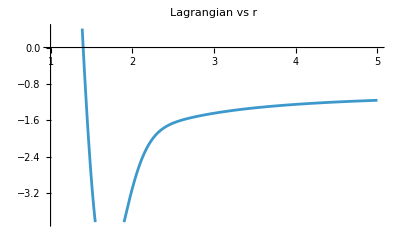

```mathematica
(*---Define Coordinates and Scalar Field---*)coords={t,r,θ,ϕ};
metric=DiagonalMatrix[{-Exp[2 Φ[r]],Exp[2 Φ[r]],r^2,r^2 Sin[θ]^2}];
invMetric=Simplify[Inverse[metric]];
Φ[r_]:=-A (1-R0/r) Exp[-(r-R0)^2/w^2];
φ[r_]:=Exp[Φ[r]]; (*scalar field for illustration*)

(*---Compute Christoffel symbols---*)
Γ=Table[Sum[1/2 invMetric[[i,k]] (D[metric[[k,j]],coords[[l]]]+D[metric[[k,l]],coords[[j]]]-D[metric[[j,l]],coords[[k]]]),{k,1,4}],{i,1,4},{j,1,4},{l,1,4}];

(*---Compute Ricci Tensor---*)
Riemann=Table[D[Γ[[i,j,k]],coords[[l]]]-D[Γ[[i,j,l]],coords[[k]]]+Sum[Γ[[i,m,k]] Γ[[m,j,l]]-Γ[[i,m,l]] Γ[[m,j,k]],{m,1,4}],{i,1,4},{j,1,4},{k,1,4},{l,1,4}];

Ricci=Table[Sum[Riemann[[m,i,m,j]],{m,1,4}],{i,1,4},{j,1,4}];

RicciScalar=Simplify[Sum[invMetric[[i,j]] Ricci[[i,j]],{i,1,4},{j,1,4}]];

(*---Kinetic Term---*)
dφ=Grad[φ[r],{r}]; (*gradient:since φ depends only on r*)
kinetic=Simplify[1/2 invMetric[[2,2]] dφ[[1]]^2]; (*Only radial term contributes*)

(*---Scalar Potential Term---*)
V[φ_]:=λ φ^4; (*Sample potential*)
potentialTerm=V[φ[r]];

(*---Full Lagrangian---*)
Lagrangian=Simplify[φ[r]^2 RicciScalar-kinetic-potentialTerm];

(*---Output---*)
Print["Ricci scalar R = ",RicciScalar];
Print["Lagrangian 𝓛 = ",Lagrangian];

Print["Limit Langarian = ",Limit[Lagrangian,r->R0]]
Print["Series Langarian = ",Series[Lagrangian,{r,∞,2}]]

Plot[Lagrangian/. {A->1,R0->1,w->0.5,λ->1},{r,1,5},PlotLabel->"Lagrangian vs r"]
```